```mathematica
(* Passband pulses with fixed profile bandwidths ϵ = 0.1, 0.2, 0.3 *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-2 and (10^-3 for N=8)*)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.01;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

PB5; p=1, 1/2, 1/4, error=0.01

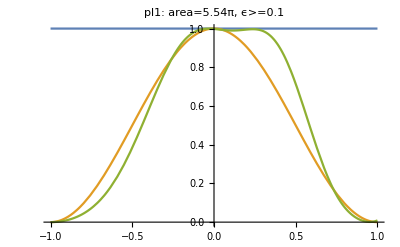

```mathematica
(*N=5 - No use*)
sequence=U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,5]]

pl1=plt[1.0,{Δ1->-2.6441,Δ2->2.1819,Δ3->-2.4579,Δ4->1.2079,Δ5->1.0844,Ω1->1.1073},"pl1"];

GGrid[Text[Style["PB5; p=1, 1/2, 1/4"<>error,FontSize->20]],{{pl1,Null,Null,Null}},ImageSize->Full]
```

PB6; p=1, 1/2, 1/4, error=0.01

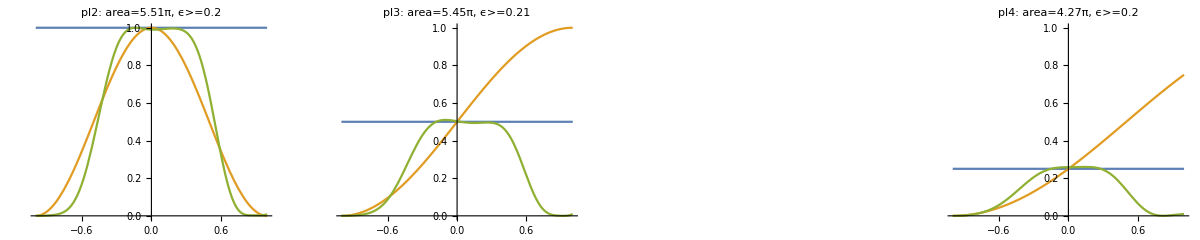

Wimperis; p=1

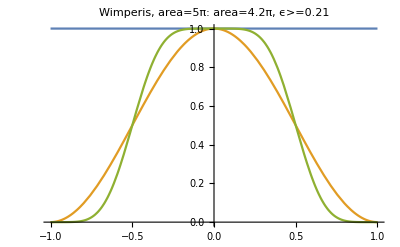

```mathematica
(*N=6 - Symmetric pulses are a bad idea*)
sequence=U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,6]]

(*pl1=plt[1.0,{Δ1->0.26964,Δ2->2.44286,Δ3->-0.01574,Δ4->0.88204,Δ5->0.37195,Δ6->-0.46059,Ω1->0.57556},"pl1"];*)
pl2=plt[1.0,{Δ1->0.1182,Δ2->-2.6317,Δ3->0.1621,Δ4->-1.1671,Δ5->0.4106,Δ6->-2.2205,Ω1->0.9187},"pl2"];

pl3=plt[0.5,{Δ1->0.9313,Δ2->-2.3469,Δ3->0.7522,Δ4->0.4524,Δ5->-2.1409,Δ6->1.0899,Ω1->0.9085},"pl3"];
pl4=plt[0.25,{Δ1->-1.9818,Δ2->0.8302,Δ3->0.6161,Δ4->-2.6083,Δ5->1.2898,Δ6->0.1399,Ω1->0.7123},"pl4"];

plt[p_,rule_,label_]:=plot[p,err,U[0,2π].U[Δ2,0].U[0,2π].U[Δ1,0].U[0,π],rule,p,label,totalArea[rule,5]]
plW=plt[1,{Δ1->2.58043,Δ2->0.83914},"Wimperis, area=5π"];

GGrid[Text[Style["PB6; p=1, 1/2, 1/4"<>error,FontSize->20]],{{pl2,pl3,Null,pl4}},ImageSize->Full]
GGrid[Text[Style["Wimperis; p=1",FontSize->20]],{{plW,Null, Null,Null}},ImageSize->Full]
```

PB7; p=1, 1/2, 1/4, error=0.01

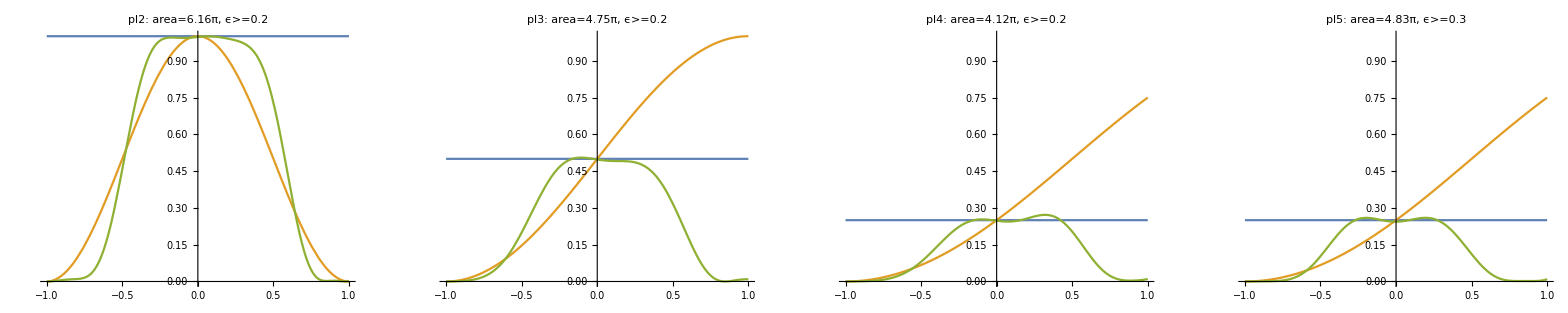

```mathematica
(*N=7*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,7]]

(*pl1=plt[1.0,{Δ1->-0.58708,Δ2->0.44134,Δ3->0.94184,Δ4->-0.07888,Δ5->2.46157,Δ6->0.14468,Δ7->2.21142,Ω1->0.57009},"pl1"];*)
pl2=plt[1.0,{Δ1->-0.956,Δ2->2.4195,Δ3->0.1351,Δ4->0.9061,Δ5->-0.4684,Δ6->2.6620,Δ7->0.2252,Ω1->0.8805},"pl2"];
pl3=plt[0.5,{Δ1->-0.3616,Δ2->-0.1652,Δ3->2.9430,Δ4->0.0601,Δ5->1.9440,Δ6->0.9139,Δ7->-0.6609,Ω1->0.6790},"pl3"];
pl4=plt[0.25,{Δ1->-2.2371,Δ2->0.0048,Δ3->2.0993,Δ4->-1.0711,Δ5->0.1657,Δ6->-0.6720,Δ7->-0.5887,Ω1->0.5887},"pl4"];
pl5=plt[0.25,{Δ1->0.7921,Δ2->-0.2430,Δ3->2.9317,Δ4->-0.1152,Δ5->0.0578,Δ6->2.6081,Δ7->0.1588,Ω1->0.6893},"pl5"];

(*(*Symmetric - Nothing found for BW>0.1, error=0.01, and for BW≥0.1, error=0.001; p=1*)
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,7]];
pl1s=pltS[1.0,{Δ1->-0.80293,Δ2->0.14347,Δ3->0.88663,Δ4->-0.03793,Ω1->0.55006},"pl1S"];*)

GGrid[Text[Style["PB7; p=1, 1/2, 1/4"<>error,FontSize->20]],{{pl2,pl3,pl4,pl5}},ImageSize->Full]
```

PB8; p=1, 1/2, 1/4, error=0.01

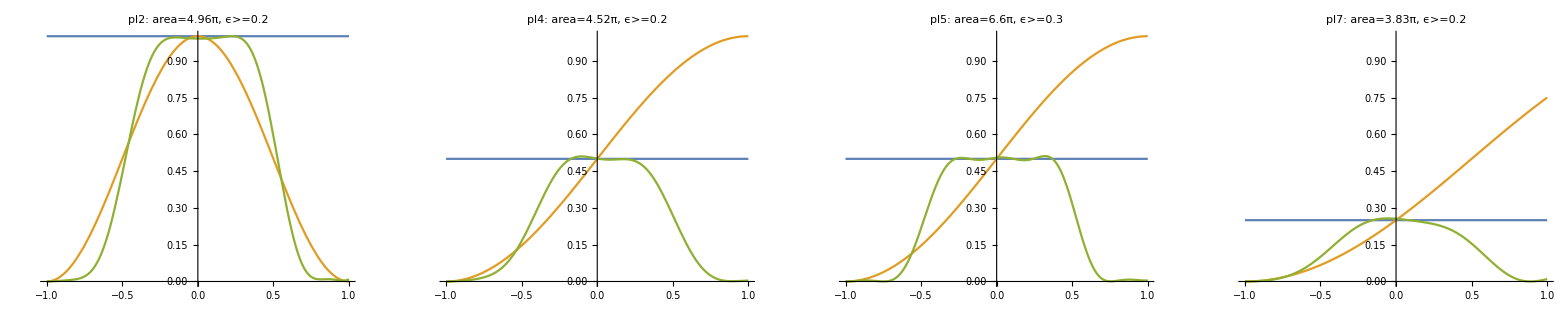

```mathematica
(*N=8 - Choose this*)
sequence=U[Δ8,Ω1].U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,8]]

(*pl1=plt[1.0,{Δ1->-0.25423,Δ2->2.47119,Δ3->-0.72405,Δ4->0.79256,Δ5->0.42896,Δ6->0.27712,Δ7->0.31048,Δ8->0.64303,Ω1->0.45199},"pl1"];*)
pl2=plt[1.0,{Δ1->0.3847,Δ2->0.5165,Δ3->-2.4852,Δ4->0.549,Δ5->0.4073,Δ6->0.3837,Δ7->0.0138,Δ8->-0.8335,Ω1->0.6197},"pl2"];

(*pl3=plt[0.5,{Δ1->0.51843,Δ2->0.41182,Δ3->0.19945,Δ4->0.75207,Δ5->0.26855,Δ6->0.2094,Δ7->0.16168,Δ8->0.65525,Ω1->0.24319},"pl3"];*)
pl4=plt[0.5,{Δ1->-0.3033,Δ2->-2.6117,Δ3->0.6058,Δ4->0.0785,Δ5->0.9827,Δ6->-2.4925,Δ7->0.7776,Δ8->-0.3939,Ω1->0.5656},"pl4"];
pl5=plt[0.5,{Δ1->2.6171,Δ2->0.5036,Δ3->0.2977,Δ4->0.1954,Δ5->0.8605,Δ6->-0.6183,Δ7->1.8844,Δ8->1.8191,Ω1->0.8250},"pl5"];

(*pl6=plt[0.25,{Δ1->0.00841,Δ2->0.16392,Δ3->0.03776,Δ4->0.18977,Δ5->0.30791,Δ6->0.14479,Δ7->0.01866,Δ8->-0.29364,Ω1->0.1072},"pl6"];*)
pl7=plt[0.25,{Δ1->2.5469,Δ2->0.3244,Δ3->-0.8225,Δ4->-0.5834,Δ5->0.3399,Δ6->-0.6677,Δ7->-0.7528,Δ8->1.0377,Ω1->0.4782},"pl7"];

GGrid[Text[Style["PB8; p=1, 1/2, 1/4"<>error,FontSize->20]],{{pl2,pl4,pl5,pl7}},ImageSize->Full]
```

PB9; p=1, 1/2, 1/4, error=0.01

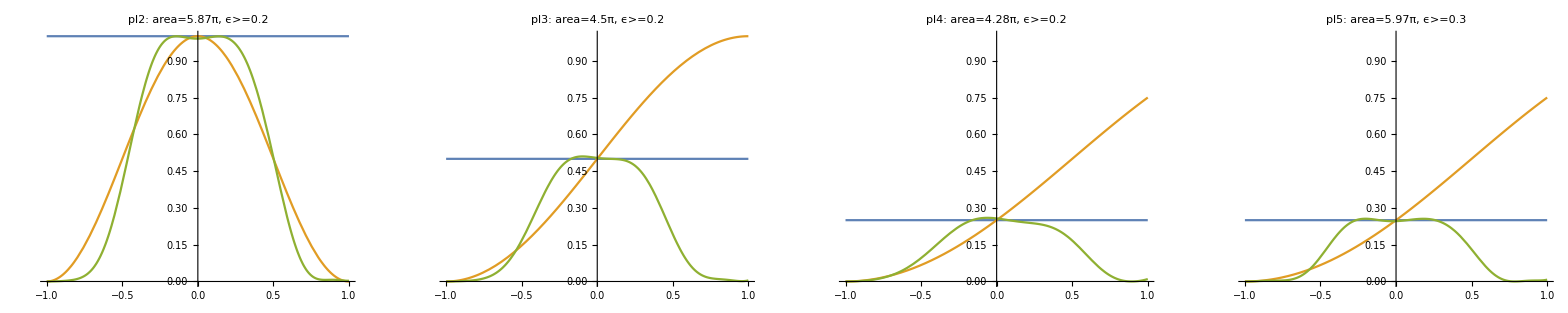

```mathematica
(*N=9*)
sequence=U[Δ9,Ω1].U[Δ8,Ω1].U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,9]]

pl2=plt[1.0,{Δ1->0.3635,Δ2->-0.2708,Δ3->-0.9648,Δ4->0.4705,Δ5->-2.4312,Δ6->2.2653,Δ7->-0.7969,Δ8->0.2874,Δ9->2.6764,Ω1->0.6519},"pl2"];

pl3=plt[0.5,{Δ1->0.5014,Δ2->0.0140,Δ3->0.6987,Δ4->1.7524,Δ5->0.3049,Δ6->0.3956,Δ7->-0.2571,Δ8->3.0466,Δ9->-0.3667,Ω1->0.5002},"pl3"];

pl4=plt[0.25,{Δ1->2.6908,Δ2->0.0338,Δ3->-0.4662,Δ4->1.1651,Δ5->0.3763,Δ6->-0.1877,Δ7->1.3033,Δ8->2.3020,Δ9->0.9639,Ω1->0.4756},"pl4"];
pl5=plt[0.25,{Δ1->0.4326,Δ2->2.1800,Δ3->-0.5480,Δ4->0.5305,Δ5->1.0676,Δ6->-0.8149,Δ7->0.9172,Δ8->-0.865,Δ9->-2.9767,Ω1->0.6637},"pl5"];

GGrid[Text[Style["PB9; p=1, 1/2, 1/4"<>error,FontSize->20]],{{pl2,pl3,pl4,pl5}},ImageSize->Full]
```

PB8; p=1, 1/2, error=0.001

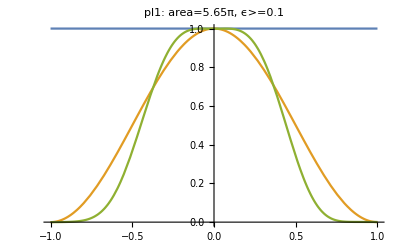

```mathematica
(*N=8*)
err=0.001;
error=", error="<>ToString@err;
sequence=U[Δ8,Ω1].U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,8]]
pl1=plt[1.0,{Δ1->-1.09477,Δ2->0.80299,Δ3->0.33117,Δ4->-2.5279,Δ5->1.18205,Δ6->3.61984,Δ7->0.69066,Δ8->-0.5203,Ω1->0.70566},"pl1"];
GGrid[Text[Style["PB8; p=1, 1/2"<>error,FontSize->20]],{{pl1,Null,Null,Null}},ImageSize->Full]
err=0.01;error=", error="<>ToString@err;
```